# Fine-Tuning Before/After Explorer

## Fine-Tuning Local LLM for Drilling & Completions -- companion notebook

This notebook uses real exported answers from this book's own base model and Chapter 5 LoRA fine-tuned checkpoint. Its job is not just to show that fine-tuning changed answers, but to make the real pattern visible: the model learned many seen training examples, still failed the held-out report, and therefore later chapters need evaluation and retrieval.

```mathematica
Main takeawayFine-tuning helped the model reproduce answers from seen training reports, but it did not give the model factual access to a report it never saw. That is why the book moves next from fine-tuning to retrieval.
```

Main takeaway
Fine-tuning helped the model reproduce answers from seen training reports, but it did not give the model factual access to a report it never saw. That is why the book moves next from fine-tuning to retrieval.

## 1. Load the real exported data

```mathematica
data = Import[FileNameJoin[{NotebookDirectory[], "data", "before_after_examples.json"}], "RawJSON"];
summary = data["summary"];
examplesList = data["examples"];
trainingExamples = Select[examplesList, #["group"] === "training" &];
heldOutExamples = Select[examplesList, #["group"] === "held_out" &];
Length[examplesList]
```

18

Helper functions used by the visual sections below.

```mathematica
ClearAll[groupLabel, statusCell, metricCard, tokenList, cleanToken, highlightedAnswer, wrappedText, shortAnswer, exampleLabel, pointLabel, questionIcon, recallValue, overlapValue, querySimilarity];

groupLabel["training"] := "Training / seen";
groupLabel["held_out"] := "Held-out / never seen";
groupLabel[g_] := g;

questionIcon["Present Ops"] := "Ops";
questionIcon["Activity Planned"] := "Plan";
questionIcon[q_] := q;

statusCell[matched_] := Framed[
  Style[If[TrueQ[matched], "MATCH", "MISS"], Bold, 11, White],
  Background -> If[TrueQ[matched], RGBColor[0.12, 0.55, 0.31], RGBColor[0.78, 0.20, 0.20]],
  FrameStyle -> None,
  RoundingRadius -> 4,
  FrameMargins -> {{8, 8}, {3, 3}}
];

metricCard[label_, value_, note_, color_] := Framed[
  Column[{Style[label, 11, GrayLevel[0.35]], Style[value, 26, Bold, color], Style[note, 10, GrayLevel[0.35]]}, Spacings -> .35],
  Background -> RGBColor[0.97, 0.97, 0.95],
  FrameStyle -> RGBColor[0.82, 0.82, 0.78],
  FrameMargins -> 12,
  RoundingRadius -> 6,
  ImageSize -> 170
];

tokenList[text_] := ToLowerCase /@ StringCases[text, WordCharacter..];
cleanToken[text_] := ToLowerCase @ StringJoin @ StringCases[text, WordCharacter..];

wrappedText[text_, width_: 560] := Pane[
  Style[text, 12, LineBreakWithin -> True],
  {width, Automatic}
];

highlightedAnswer[answer_, expected_] := Module[
  {expectedTokens = DeleteDuplicates[tokenList[expected]], words, styledWords},
  words = StringSplit[answer];
  styledWords = If[MemberQ[expectedTokens, cleanToken[#]],
      Style[#, Bold, RGBColor[0.05, 0.45, 0.22], Background -> RGBColor[0.88, 0.97, 0.90]],
      Style[#, 12]
    ] & /@ words;
  Pane[
    Grid[Partition[styledWords, UpTo[7]], Alignment -> Left, Spacings -> {.35, .25}],
    {560, Automatic}
  ]
];

shortAnswer[text_, n_: 95] := If[StringLength[text] <= n, text, StringTake[text, n] <> "..."];
recallValue[ex_, model_] := ex[model <> "_metrics"]["expected_token_recall"];
overlapValue[ex_, model_] := ex[model <> "_metrics"]["jaccard_overlap"];
querySimilarity[ex_, key_] := ex["query_similarity"][key];

exampleLabel[ex_] := "Report #" <> ex["report_number"] <> " | " <> ex["question_type"] <> " | " <> groupLabel[ex["group"]];
pointLabel[ex_, model_] := exampleLabel[ex] <> "\n" <> If[model === "base", "Before", "After"] <> " word overlap: " <> ToString[NumberForm[recallValue[ex, model], {3, 2}]];
```

## 2. Executive view: what changed?

The headline is intentionally split into seen training questions and a never-seen held-out report. This is the key distinction: fine-tuning improved word overlap on examples like the ones it studied, but it did not create a grounded memory of the held-out report.

```mathematica
Grid[
  {{
    metricCard["Training before", ToString[summary["training_before"]] <> "/" <> ToString[summary["training_total"]], "base model exact matches", RGBColor[0.75, 0.18, 0.18]],
    metricCard["Training after", ToString[summary["training_after"]] <> "/" <> ToString[summary["training_total"]], "fine-tuned exact matches", RGBColor[0.08, 0.47, 0.25]],
    metricCard["Held-out before", ToString[summary["held_out_before"]] <> "/" <> ToString[summary["held_out_total"]], "never seen by training", RGBColor[0.75, 0.18, 0.18]],
    metricCard["Held-out after", ToString[summary["held_out_after"]] <> "/" <> ToString[summary["held_out_total"]], "still no exact matches", RGBColor[0.75, 0.18, 0.18]]
  }},
  Spacings -> {1.2, 1}
]
```

Training before
0/16
base model exact matches | Training after
13/16
fine-tuned exact matches | Held-out before
0/2
never seen by training | Held-out after
0/2
still no exact matches

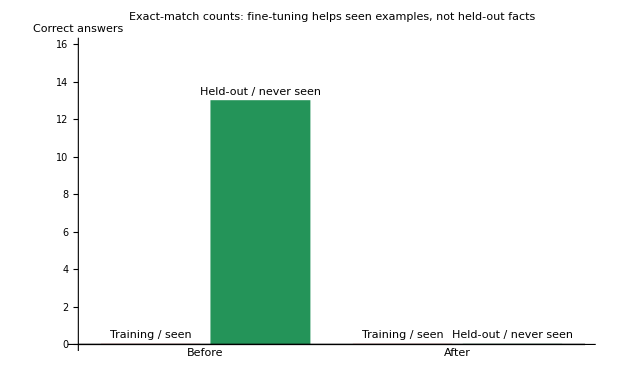

```mathematica
BarChart[
  {
    {summary["training_before"], summary["training_after"]},
    {summary["held_out_before"], summary["held_out_after"]}
  },
  ChartLabels -> {Placed[{"Before", "After"}, Below], Placed[{"Training / seen", "Held-out / never seen"}, Above]},
  ChartStyle -> {RGBColor[0.82, 0.28, 0.23], RGBColor[0.14, 0.58, 0.35]},
  PlotLabel -> "Exact-match counts: fine-tuning helps seen examples, not held-out facts",
  AxesLabel -> {None, "Correct answers"},
  ImageSize -> 620,
  PlotRange -> {0, summary["training_total"]}
]
```

## 3. Outcome map: all questions at once

This compact map makes the pattern visible without clicking through examples one by one. Green means the answer exactly contained the reference wording. The word-overlap columns show how much of the correct answer's vocabulary appears in each model answer, which helps separate total misses from near misses.

```mathematica
Grid[
  Prepend[
    Table[
      {
        Style["#" <> ToString[i], GrayLevel[0.35]],
        Style[groupLabel[examplesList[[i]]["group"]], 11],
        "Report #" <> examplesList[[i]]["report_number"],
        questionIcon[examplesList[[i]]["question_type"]],
        statusCell[examplesList[[i]]["base_matched"]],
        statusCell[examplesList[[i]]["finetuned_matched"]],
        NumberForm[recallValue[examplesList[[i]], "base"], {3, 2}],
        NumberForm[recallValue[examplesList[[i]], "finetuned"], {3, 2}],
        Style[examplesList[[i]]["failure_category"], 10, GrayLevel[0.25]]
      },
      {i, Length[examplesList]}
    ],
    {Style["Row", Bold], Style["Set", Bold], Style["Report", Bold], Style["Question", Bold], Style["Before", Bold], Style["After", Bold], Style["Before word overlap", Bold], Style["After word overlap", Bold], Style["Reading", Bold]}
  ],
  Alignment -> Left,
  Dividers -> {None, {True, True}},
  Spacings -> {1.2, .7},
  Background -> {None, {RGBColor[0.92, 0.92, 0.88], None}}
]
```

Row | Set | Report | Question | Before | After | Before word overlap | After word overlap | Reading
#1 | Training / seen | Report #3 | Ops | MISS | MATCH | 0.10 | 1.00 | Exact match after fine-tuning
#2 | Training / seen | Report #3 | Plan | MISS | MISS | 0.18 | 0.09 | Partial wording overlap, wrong answer
#3 | Training / seen | Report #19 | Ops | MISS | MATCH | 0.00 | 1.00 | Exact match after fine-tuning
#4 | Training / seen | Report #19 | Plan | MISS | MATCH | 0.13 | 1.00 | Exact match after fine-tuning
#5 | Training / seen | Report #36 | Ops | MISS | MISS | 0.00 | 0.00 | Wrong memorized pattern
#6 | Training / seen | Report #36 | Plan | MISS | MATCH | 0.20 | 1.00 | Exact match after fine-tuning
#7 | Training / seen | Report #38 | Ops | MISS | MATCH | 0.22 | 1.00 | Exact match after fine-tuning
#8 | Training / seen | Report #38 | Plan | MISS | MATCH | 0.00 | 1.00 | Exact match after fine-tuning
#9 | Training / seen | Report #39 | Ops | MISS | MATCH | 0.00 | 1.00 | Exact match after fine-tuning
#10 | Training / seen | Report #39 | Plan | MISS | MATCH | 0.00 | 1.00 | Exact match after fine-tuning
#11 | Training / seen | Report #48 | Ops | MISS | MISS | 0.00 | 0.00 | Wrong memorized pattern
#12 | Training / seen | Report #48 | Plan | MISS | MATCH | 0.00 | 1.00 | Exact match after fine-tuning
#13 | Training / seen | Report #49 | Ops | MISS | MATCH | 0.33 | 1.00 | Exact match after fine-tuning
#14 | Training / seen | Report #49 | Plan | MISS | MATCH | 0.00 | 1.00 | Exact match after fine-tuning
#15 | Training / seen | Report #50 | Ops | MISS | MATCH | 0.00 | 1.00 | Exact match after fine-tuning
#16 | Training / seen | Report #50 | Plan | MISS | MATCH | 0.00 | 1.00 | Exact match after fine-tuning
#17 | Held-out / never seen | Report #37 | Ops | MISS | MISS | 0.14 | 0.00 | Held-out generalization gap
#18 | Held-out / never seen | Report #37 | Plan | MISS | MISS | 0.00 | 0.08 | Held-out generalization gap

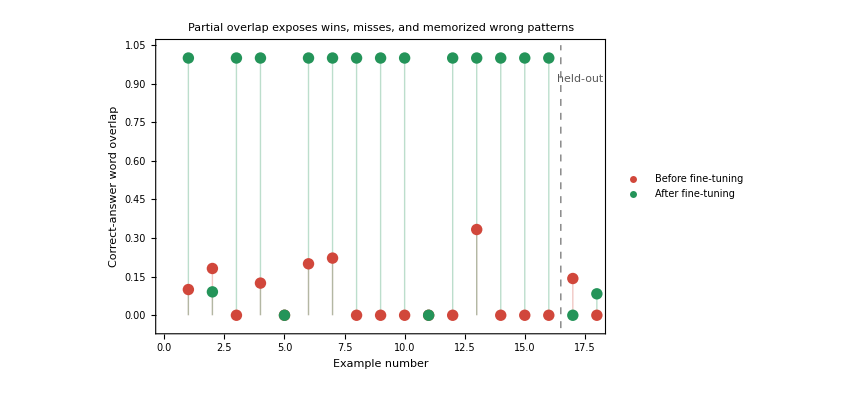

```mathematica
ListPlot[
  {
    Table[Tooltip[{i, recallValue[examplesList[[i]], "base"]}, pointLabel[examplesList[[i]], "base"]], {i, Length[examplesList]}],
    Table[Tooltip[{i, recallValue[examplesList[[i]], "finetuned"]}, pointLabel[examplesList[[i]], "finetuned"]], {i, Length[examplesList]}]
  },
  PlotLegends -> {"Before fine-tuning", "After fine-tuning"},
  PlotStyle -> {RGBColor[0.82, 0.28, 0.23], RGBColor[0.14, 0.58, 0.35]},
  Filling -> Axis,
  Frame -> True,
  FrameLabel -> {"Example number", "Correct-answer word overlap"},
  PlotLabel -> "Partial overlap exposes wins, misses, and memorized wrong patterns",
  ImageSize -> 640,
  PlotRange -> {-0.05, 1.05},
  Epilog -> {
    Dashed, GrayLevel[0.5],
    Line[{{Length[trainingExamples] + .5, -0.05}, {Length[trainingExamples] + .5, 1.05}}],
    Text[Style["held-out", 11, GrayLevel[0.35]], {Length[trainingExamples] + 1.3, .92}]
  }
]
```

## 4. Query-to-answer cosine similarity

Cosine similarity compares the words in the query with the words in each answer. It is useful for spotting answers that echo the question, but it is not a correctness score. In this notebook, correctness still comes from matching the reference answer and reading the source excerpt.

```mathematica
cosineRows = Table[
  {
    Style["#" <> ToString[i], GrayLevel[0.35]],
    Style[exampleLabel[examplesList[[i]]], 11],
    NumberForm[querySimilarity[examplesList[[i]], "query_to_reference"], {3, 2}],
    NumberForm[querySimilarity[examplesList[[i]], "query_to_base_answer"], {3, 2}],
    NumberForm[querySimilarity[examplesList[[i]], "query_to_finetuned_answer"], {3, 2}],
    Style[If[
      querySimilarity[examplesList[[i]], "query_to_base_answer"] > querySimilarity[examplesList[[i]], "query_to_finetuned_answer"],
      "Base echoes query more",
      "Fine-tuned echoes query more"
    ], 10, GrayLevel[0.25]]
  },
  {i, Length[examplesList]}
];

Grid[
  Prepend[
    cosineRows,
    {Style["Row", Bold], Style["Example", Bold], Style["Query vs reference", Bold], Style["Query vs base", Bold], Style["Query vs fine-tuned", Bold], Style["Reading", Bold]}
  ],
  Alignment -> Left,
  Dividers -> {None, {True, True}},
  Spacings -> {1.1, .7},
  Background -> {None, {RGBColor[0.92, 0.92, 0.88], None}}
]
```

Row | Example | Query vs reference | Query vs base | Query vs fine-tuned | Reading
#1 | Report #3 | Present Ops | Training / seen | 0.00 | 0.49 | 0.00 | Base echoes query more
#2 | Report #3 | Activity Planned | Training / seen | 0.00 | 0.16 | 0.00 | Base echoes query more
#3 | Report #19 | Present Ops | Training / seen | 0.00 | 0.49 | 0.00 | Base echoes query more
#4 | Report #19 | Activity Planned | Training / seen | 0.00 | 0.20 | 0.00 | Base echoes query more
#5 | Report #36 | Present Ops | Training / seen | 0.00 | 0.60 | 0.00 | Base echoes query more
#6 | Report #36 | Activity Planned | Training / seen | 0.00 | 0.31 | 0.00 | Base echoes query more
#7 | Report #38 | Present Ops | Training / seen | 0.00 | 0.49 | 0.00 | Base echoes query more
#8 | Report #38 | Activity Planned | Training / seen | 0.00 | 0.31 | 0.00 | Base echoes query more
#9 | Report #39 | Present Ops | Training / seen | 0.00 | 0.49 | 0.00 | Base echoes query more
#10 | Report #39 | Activity Planned | Training / seen | 0.00 | 0.31 | 0.00 | Base echoes query more
#11 | Report #48 | Present Ops | Training / seen | 0.00 | 0.41 | 0.00 | Base echoes query more
#12 | Report #48 | Activity Planned | Training / seen | 0.00 | 0.25 | 0.00 | Base echoes query more
#13 | Report #49 | Present Ops | Training / seen | 0.00 | 0.41 | 0.00 | Base echoes query more
#14 | Report #49 | Activity Planned | Training / seen | 0.00 | 0.25 | 0.00 | Base echoes query more
#15 | Report #50 | Present Ops | Training / seen | 0.00 | 0.41 | 0.00 | Base echoes query more
#16 | Report #50 | Activity Planned | Training / seen | 0.00 | 0.25 | 0.00 | Base echoes query more
#17 | Report #37 | Present Ops | Held-out / never seen | 0.00 | 0.60 | 0.00 | Base echoes query more
#18 | Report #37 | Activity Planned | Held-out / never seen | 0.00 | 0.31 | 0.00 | Base echoes query more

```mathematica
cosineOptions = Table[i -> exampleLabel[examplesList[[i]]], {i, Length[examplesList]}];

Manipulate[
  Module[{ex = examplesList[[i]], values},
    values = {
      querySimilarity[ex, "query_to_reference"],
      querySimilarity[ex, "query_to_base_answer"],
      querySimilarity[ex, "query_to_finetuned_answer"]
    };
    Column[{
      Framed[
        Column[{
          Style[exampleLabel[ex], 14, Bold],
          Style["Query text", Bold],
          Panel[wrappedText[ex["query_text"], 650]],
          Style["How much each answer reuses the query wording", Bold]
        }, Spacings -> .7],
        Background -> RGBColor[0.97, 0.97, 0.95],
        FrameStyle -> RGBColor[0.82, 0.82, 0.78],
        FrameMargins -> 12,
        RoundingRadius -> 6
      ],
      BarChart[
        values,
        ChartLabels -> Placed[{"Reference", "Base answer", "Fine-tuned answer"}, Below],
        ChartStyle -> {RGBColor[0.35, 0.48, 0.78], RGBColor[0.82, 0.28, 0.23], RGBColor[0.14, 0.58, 0.35]},
        PlotRange -> {0, 1},
        AxesLabel -> {None, "Cosine similarity to query"},
        PlotLabel -> "Query-to-answer lexical cosine similarity",
        ImageSize -> 620
      ],
      Style[
        "Read this as prompt-word similarity, not correctness. A high base score can mean the base model repeated the question context instead of answering from the report.",
        11,
        GrayLevel[0.35]
      ]
    }, Spacings -> 1.1]
  ],
  {{i, 1, "Pick a real query"}, cosineOptions},
  ControlPlacement -> Top
]
```

## 5. Guided examples: one win, one limit

These two examples are the shortest path through the result. The first shows what fine-tuning learned well. The second shows the limit: a held-out report still needs retrieval because its facts were never in the training examples.

```mathematica
successExample = FirstCase[examplesList, ex_ /; ex["group"] === "training" && TrueQ[ex["finetuned_matched"]] && ! TrueQ[ex["base_matched"]] :> ex];
heldOutFailureExample = FirstCase[examplesList, ex_ /; ex["group"] === "held_out" && ! TrueQ[ex["finetuned_matched"]] :> ex];

guidedCard[title_, ex_, color_, note_] := Framed[
  Module[{fieldWidth = 455, fieldBlock, scoreLine},
    fieldBlock[label_, body_] := Column[
      {
        Style[label, Bold],
        Panel[wrappedText[body, fieldWidth]]
      },
      Spacings -> .25
    ];
    scoreLine[label_, matched_, value_] := Row[
      {Style[label, Bold], Spacer[10], statusCell[matched], Spacer[8], NumberForm[value, {3, 2}], " word overlap"}
    ];
    Column[{
      Style[title, 16, Bold, color],
      Style[exampleLabel[ex], 12, GrayLevel[0.35]],
      fieldBlock["Question", ex["instruction"]],
      fieldBlock["Expected", ex["expected"]],
      scoreLine["Before", ex["base_matched"], recallValue[ex, "base"]],
      fieldBlock["Why base missed", ex["base_miss_explanation"]],
      scoreLine["After", ex["finetuned_matched"], recallValue[ex, "finetuned"]],
      fieldBlock["After answer", ex["finetuned_model_answer"]],
      fieldBlock["Takeaway", note]
    }, Spacings -> .75]
  ],
  Background -> RGBColor[0.98, 0.98, 0.96],
  FrameStyle -> Lighter[color, .55],
  FrameMargins -> 12,
  RoundingRadius -> 6,
  ImageSize -> 540
];

Grid[
  {{
    guidedCard[
      "What fine-tuning learned",
      successExample,
      RGBColor[0.05, 0.42, 0.22],
      "The fine-tuned model reproduces the expected report wording exactly on a seen training-style example."
    ],
    guidedCard[
      "What fine-tuning still cannot know",
      heldOutFailureExample,
      RGBColor[0.72, 0.18, 0.16],
      "This report was never seen during training, so the fine-tuned answer remains ungrounded. This is the handoff point to retrieval."
    ]
  }},
  Spacings -> {1.4, 1}
]
```

What fine-tuning learned
Report #3 | Present Ops | Training / seen
Question
What are the present operations reported on this well?
Expected
RIGGING UP WITH FRONTIER CREWS AND SUPERVISION AND JW JONES TRUCKING
BeforeMISS0.10 word overlap
Why base missed
The base prompt only includes the well name, report number, date, and question. It does not include the report field containing the correct answer, so the base model has no source text to extract from. The generated base answer also stops mid-sentence, which shows the output was cut off by the generation limit rather than reaching a complete answer.
AfterMATCH1.00 word overlap
After answer
RIGGING UP WITH FRONTIER CREWS AND SUPERVISION AND JW JONES TRUCKING
Takeaway
The fine-tuned model reproduces the expected report wording exactly on a seen training-style example. | What fine-tuning still cannot know
Report #37 | Present Ops | Held-out / never seen
Question
What are the present operations reported on this well?
Expected
RIG UP SCHLUMBERGER PREPARE TO RUN LOGS
BeforeMISS0.14 word overlap
Why base missed
The base prompt only includes the well name, report number, date, and question. It does not include the report field containing the correct answer, so the base model has no source text to extract from.
AfterMISS0.00 word overlap
After answer
PIPE FREE, TRIP OUT OF HOLE FOR BHA INSPECTION
Takeaway
This report was never seen during training, so the fine-tuned answer remains ungrounded. This is the handoff point to retrieval.

## 6. Answer microscope

Pick any real question. Highlighted words are tokens that also appear in the reference answer. This turns the before/after comparison into something you can read visually: generic explanations, exact copied successes, and confident wrong template reuse look very different.

```mathematica
optionsList = Table[i -> exampleLabel[examplesList[[i]]], {i, Length[examplesList]}];

Manipulate[
  Module[{ex = examplesList[[i]]},
    Column[{
      Framed[
        Grid[{
          {Style["Question", Bold, 13], ex["instruction"]},
          {Style["Context", Bold, 13], ex["report_context"]},
          {Style["Set", Bold, 13], groupLabel[ex["group"]]},
          {Style["Outcome", Bold, 13], Row[{"Before ", statusCell[ex["base_matched"]], Spacer[12], "After ", statusCell[ex["finetuned_matched"]]}]}
        }, Alignment -> Left, Spacings -> {1.2, .75}],
        Background -> RGBColor[0.97, 0.97, 0.95],
        FrameStyle -> RGBColor[0.82, 0.82, 0.78],
        RoundingRadius -> 6,
        FrameMargins -> 12
      ],

      Style["Source report excerpt", Bold, 14],
      Panel[Pane[Style[ex["snippet"], FontFamily -> "Courier", FontSize -> 12], {680, 145}, Scrollbars -> True]],

      Style["Reference answer", Bold, 14],
      Framed[Style[ex["expected"], 13, RGBColor[0.1, 0.1, 0.1]], Background -> RGBColor[0.94, 0.96, 1.0], FrameStyle -> RGBColor[0.75, 0.80, 0.90], FrameMargins -> 10],

      Style["Why the base model missed", Bold, 14],
      Framed[
        wrappedText[ex["base_miss_explanation"], 680],
        Background -> RGBColor[1.0, 0.97, 0.92],
        FrameStyle -> RGBColor[0.90, 0.72, 0.55],
        FrameMargins -> 10,
        RoundingRadius -> 6
      ],

      Grid[
        {
          {
            Style["Base model before fine-tuning", Bold, RGBColor[0.65, 0.12, 0.12]],
            Style["Fine-tuned model after fine-tuning", Bold, RGBColor[0.05, 0.40, 0.22]]
          },
          {
            Panel[highlightedAnswer[ex["base_model_answer"], ex["expected"]], ImageSize -> 340],
            Panel[highlightedAnswer[ex["finetuned_model_answer"], ex["expected"]], ImageSize -> 340]
          },
          {
            Row[{"Correct-answer word overlap: ", NumberForm[recallValue[ex, "base"], {3, 2}], " | Query cosine: ", NumberForm[querySimilarity[ex, "query_to_base_answer"], {3, 2}]}],
            Row[{"Correct-answer word overlap: ", NumberForm[recallValue[ex, "finetuned"], {3, 2}], " | Query cosine: ", NumberForm[querySimilarity[ex, "query_to_finetuned_answer"], {3, 2}]}]
          }
        },
        Alignment -> Left,
        Spacings -> {2, 1},
        Dividers -> Center
      ]
    }, Spacings -> 1.2]
  ],
  {{i, 1, "Pick a real question"}, optionsList},
  ControlPlacement -> Top
]
```

## 7. Failure patterns

The failures after fine-tuning are the most important teaching examples. They show that the fine-tuned model can sound more domain-specific while still pulling the wrong remembered pattern into a new report context.

```mathematica
failedAfter = Select[examplesList, ! TrueQ[#["finetuned_matched"]] &];
failureOptions = Table[i -> exampleLabel[failedAfter[[i]]] <> " | " <> failedAfter[[i]]["failure_category"], {i, Length[failedAfter]}];

Manipulate[
  Module[{ex = failedAfter[[i]]},
    Column[{
      Framed[
        Column[{
          Style[ex["failure_category"], 16, Bold, RGBColor[0.65, 0.15, 0.12]],
          Style[exampleLabel[ex], 12, GrayLevel[0.25]]
        }],
        Background -> RGBColor[1.0, 0.95, 0.92],
        FrameStyle -> RGBColor[0.90, 0.68, 0.60],
        FrameMargins -> 12,
        RoundingRadius -> 6
      ],
      Grid[
        {
          {Style["Expected from report", Bold], Panel[wrappedText[ex["expected"], 620]]},
          {Style["Fine-tuned answer", Bold], Panel[highlightedAnswer[ex["finetuned_model_answer"], ex["expected"]]]},
          {Style["What to notice", Bold], If[ex["group"] === "held_out",
              "The model never saw this report during training. Fine-tuning alone did not give it factual access to the held-out report.",
              "The answer is now domain-shaped, but it is the wrong report pattern. This is more convincing than the base model, and therefore more dangerous."
            ]}
        },
        Alignment -> Left,
        Spacings -> {1.2, 1}
      ]
    }, Spacings -> 1.2]
  ],
  {{i, 1, "Post-fine-tune failure"}, failureOptions},
  ControlPlacement -> Top
]
```

## 8. Optional advanced: semantic embeddings

This optional section uses a sentence-embedding model to compare meanings rather than exact words. It is useful for spotting answers that are conceptually close to the reference even when exact-match says MISS. It is still not a factual correctness score: an answer can be semantically oilfield-like and still refer to the wrong report.

```mathematica
semanticPath = FileNameJoin[{NotebookDirectory[], "data", "semantic_embedding_examples.json"}];

If[! FileExistsQ[semanticPath],
  Framed[
    Column[{
      Style["Optional semantic embedding data not found", 15, Bold],
      "Run this from the repository root to generate it:",
      Style["python mathematica/export_semantic_embeddings.py", FontFamily -> "Courier", 12],
      "The first run may download the sentence-transformer model used in Chapter 4."
    }, Spacings -> .7],
    Background -> RGBColor[1.0, 0.98, 0.92],
    FrameStyle -> RGBColor[0.86, 0.72, 0.45],
    FrameMargins -> 14,
    RoundingRadius -> 6
  ],

  semanticData = Import[semanticPath, "RawJSON"];
  semanticExamples = semanticData["examples"];
  semanticPoints = semanticData["points_2d"];

  Column[{
    Framed[
      Column[{
        Style["Semantic model", 14, Bold],
        semanticData["model"],
        Style[semanticData["note"], 11, GrayLevel[0.35]]
      }, Spacings -> .5],
      Background -> RGBColor[0.95, 0.97, 1.0],
      FrameStyle -> RGBColor[0.70, 0.78, 0.90],
      FrameMargins -> 12,
      RoundingRadius -> 6
    ],

    Grid[
      Prepend[
        Table[
          {
            Style["#" <> ToString[row["row"]], GrayLevel[0.35]],
            row["label"],
            NumberForm[row["semantic_similarity"]["base_answer_to_reference"], {3, 2}],
            NumberForm[row["semantic_similarity"]["finetuned_answer_to_reference"], {3, 2}],
            If[row["semantic_similarity"]["finetuned_answer_to_reference"] > row["semantic_similarity"]["base_answer_to_reference"],
              Style["Fine-tuned closer", RGBColor[0.05, 0.40, 0.22]],
              Style["Base closer", RGBColor[0.65, 0.12, 0.12]]
            ]
          },
          {row, semanticExamples}
        ],
        {Style["Row", Bold], Style["Example", Bold], Style["Base vs reference", Bold], Style["Fine-tuned vs reference", Bold], Style["Reading", Bold]}
      ],
      Alignment -> Left,
      Dividers -> {None, {True, True}},
      Spacings -> {1.1, .7},
      Background -> {None, {RGBColor[0.92, 0.92, 0.88], None}}
    ],

    ListPlot[
      Table[
        Tooltip[
          {point["x"], point["y"]},
          point["label"]
        ],
        {point, semanticPoints}
      ],
      PlotStyle -> GrayLevel[0.25],
      Frame -> True,
      FrameLabel -> {"Embedding projection 1", "Embedding projection 2"},
      PlotLabel -> "2D projection of queries, references, and model answers",
      ImageSize -> 640
    ]
  }, Spacings -> 1.2]
]
```

Optional semantic embedding data not found
Run this from the repository root to generate it:
python mathematica/export_semantic_embeddings.py
The first run may download the sentence-transformer model used in Chapter 4.

```mathematica
Null
```

## 9. Why retrieval comes next

This Chapter 5 notebook deliberately stops at fine-tuning, but the visual result points toward Chapter 9: when the report was never in training, the model needs a retrieval step to find the relevant source text before answering.

```mathematica
heldOutPanel = Framed[
  Column[{
    Style["Held-out report #37 remains unsolved by fine-tuning alone", 15, Bold],
    "Fine-tuning changed the model's style and made many seen examples exact. It did not make unseen report facts available inside the weights.",
    "Next visual extension: add a third answer lane for Fine-tuned + retrieval, with the retrieved source chunk shown beside the generated answer."
  }, Spacings -> .8],
  Background -> RGBColor[0.95, 0.97, 1.0],
  FrameStyle -> RGBColor[0.70, 0.78, 0.90],
  FrameMargins -> 14,
  RoundingRadius -> 6
];

If[Length[heldOutExamples] > 0,
  Column[{
    heldOutPanel,
    Grid[
      Prepend[
        Table[
          {
            "Report #" <> ex["report_number"],
            ex["question_type"],
            statusCell[ex["finetuned_matched"]],
            shortAnswer[ex["expected"], 75],
            shortAnswer[ex["finetuned_model_answer"], 75]
          },
          {ex, heldOutExamples}
        ],
        {Style["Report", Bold], Style["Question", Bold], Style["Fine-tuned", Bold], Style["Reference", Bold], Style["Fine-tuned answer", Bold]}
      ],
      Alignment -> Left,
      Spacings -> {1.2, .8},
      Dividers -> {None, {True, True}}
    ]
  }, Spacings -> 1.2],
  heldOutPanel
]
```

Held-out report #37 remains unsolved by fine-tuning alone
Fine-tuning changed the model's style and made many seen examples exact. It did not make unseen report facts available inside the weights.
Next visual extension: add a third answer lane for Fine-tuned + retrieval, with the retrieved source chunk shown beside the generated answer.
Report | Question | Fine-tuned | Reference | Fine-tuned answer
Report #37 | Present Ops | MISS | RIG UP SCHLUMBERGER PREPARE TO RUN LOGS | PIPE FREE, TRIP OUT OF HOLE FOR BHA INSPECTION
Report #37 | Activity Planned | MISS | RUN UBI LOG, PICK UP BHA # 2, DRILL 8 3/4" Curve | CONTINUE BUILDING CURVE TO 65°

To regenerate this data yourself -- for example after retraining Chapter 5's checkpoint, or against your own reports -- run "python mathematica/export_before_after.py" from the repository root, with book/.venv active. See mathematica/README.md for details and prerequisites.